# Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Options[plotGrid]={ImagePadding->30};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
max[data_] := Sort[data,#1[[2]]>#2[[2]]&][[1]]
```

```mathematica
𝒜 [bm_,bp_]:=(bm-bp)/(bp+bm); 
σ𝒜 [bm_,σbm_,bp_,σbp_]:=Sqrt[((bp-bm)/(bp+bm)^2-1/(bp+bm))^2*σbp^2 +((bp-bm)/(bp+bm)^2+1/(bp+bm))^2*σbm^2 ]; 
out[b_,σb_,str_] := Text[Style[str  <>ToString@b <> "±" <> ToString@σb,Black, 20]];
```

# Plotting the BDT Cuts and FOM for Run 1

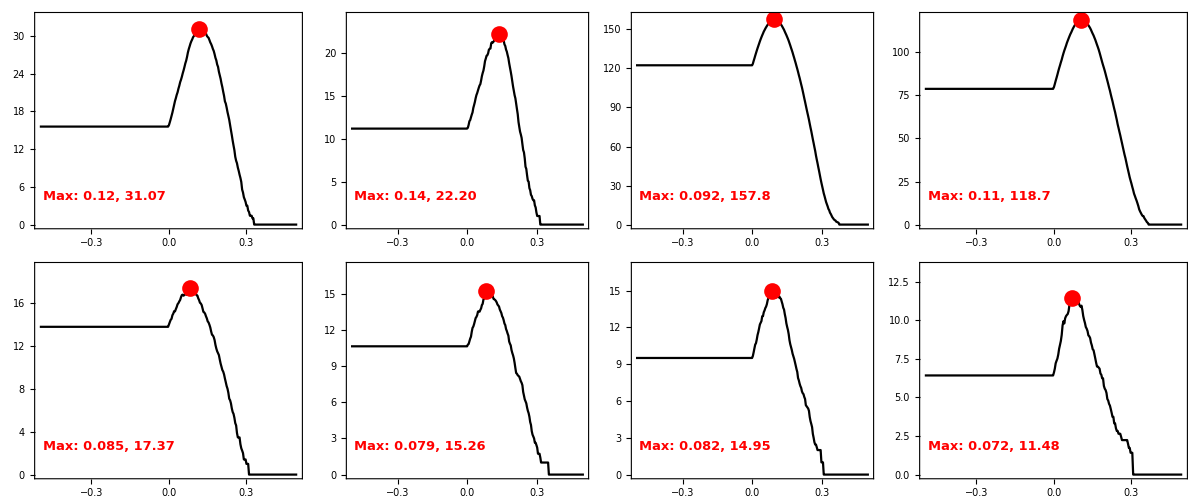
-Graphics-S/√(S + B)BDT Cut

grid.pdf

```mathematica
data0=Import["run1/fom_0.csv","Data"];data0=Transpose[data0];
data1=Import["run1/fom_1.csv","Data"];data1=Transpose[data1];
data2=Import["run1/fom_2.csv","Data"];data2=Transpose[data2];
data3=Import["run1/fom_3.csv","Data"];data3=Transpose[data3];
data4=Import["run1/fom_4.csv","Data"];data4=Transpose[data4];
data5=Import["run1/fom_5.csv","Data"];data5=Transpose[data5];
data6=Import["run1/fom_6.csv","Data"];data6=Transpose[data6];
data7=Import["run1/fom_7.csv","Data"];data7=Transpose[data7];
alldata = {data0, data1, data2, data3, data4, data5, data6, data7};
maxima = {max[data0],max[data1],max[data2],max[data3],max[data4],max[data5],max[data6],max[data7]};

labels = {"a)", "b)","c)","d)","e)","f)","g)", "h)"};
plots = Table[ListLinePlot[alldata[[i]],PlotStyle->{Black}, PlotRange->{0,maxima[[i]][[2]] + 2}, Frame->True,FrameStyle->Directive[15, Black],Axes->False, FrameTicks->All, PlotRangePadding->{0.2,2},Epilog->{Text[Style["Max: " <>ToString@ N[maxima[[i]][[1]],2]<>", "<>ToString@N[maxima[[i]][[2]],4],13, Bold,Red],Scaled[{0.03,0.15}],{-1,0}],Red,PointSize[0.03],Point@maxima[[i]]}],{i,1,8}];
plots = Partition[plots, 4];

grid = plotGrid[plots, 1200, 500];
Labeled[grid, {"S/√(S + B)","BDT Cut"},{Left, Bottom},LabelStyle->Directive[20, Black], RotateLabel->True]
Export["grid.png",%]
```

# Calculating the CP Asymmetries for Run 1

```mathematica
data0=Flatten[Import["run1/cp_0.csv","Data"]];
data1=Flatten[Import["run1/cp_1.csv","Data"]];
data2=Flatten[Import["run1/cp_2.csv","Data"]];
data3=Flatten[Import["run1/cp_3.csv","Data"]];
data4=Flatten[Import["run1/cp_4.csv","Data"]];
data5=Flatten[Import["run1/cp_5.csv","Data"]];
data6=Flatten[Import["run1/cp_6.csv","Data"]];
data7=Flatten[Import["run1/cp_7.csv","Data"]];
```

```mathematica
dpData = {data0[[1]]+data1[[1]], data0[[3]]+data1[[3]]};
dpErro = {Sqrt[data0[[2]]^2+data1[[2]]^2],Sqrt[data0[[4]]^2+data1[[4]]^2]};
𝒜DP = 𝒜[dpData[[1]],dpData[[2]]];
σ𝒜DP = σ𝒜[dpData[[1]],dpErro[[1]],dpData[[2]],dpErro[[2]]];
out[N[𝒜DP,2], N[σ𝒜DP,2] , "The D^+ asymmetry: "]
```

The D^+ asymmetry: 0.0063±0.023

```mathematica
dsData = {data2[[1]]+data3[[1]], data2[[3]]+data3[[3]]};
dsErro = {Sqrt[data2[[2]]^2+data3[[2]]^2],Sqrt[data2[[4]]^2+data3[[4]]^2]};
𝒜DS = 𝒜[dsData[[1]],dsData[[2]]];
σ𝒜DS = σ𝒜[dsData[[1]],dsErro[[1]],dsData[[2]],dsErro[[2]]];
out[N[𝒜DS,2], N[σ𝒜DS,2] , "The D_s^+ asymmetry: "]
```

The D_s^+ asymmetry: 0.018±0.0049

```mathematica
dtData = {data4[[1]]+data5[[1]]+data6[[1]]+data7[[1]], data4[[3]]+data5[[3]]+data6[[3]]+data7[[3]]};
dtErro = {Sqrt[data4[[2]]^2+data5[[2]]^2+data6[[2]]^2+data7[[2]]^2],Sqrt[data4[[4]]^2+data5[[4]]^2+data6[[4]]^2+data7[[4]]^2]};
𝒜DT = 𝒜[dtData[[1]],dtData[[2]]];
σ𝒜DT = σ𝒜[dtData[[1]],dtErro[[1]],dtData[[2]],dtErro[[2]]];
out[N[𝒜DT,2], N[σ𝒜DT,2] , "The D^(*+) asymmetry: "]
```

The D^(*+) asymmetry: -0.023±0.032

# Plotting the BDT Cuts and FOM for Run 2

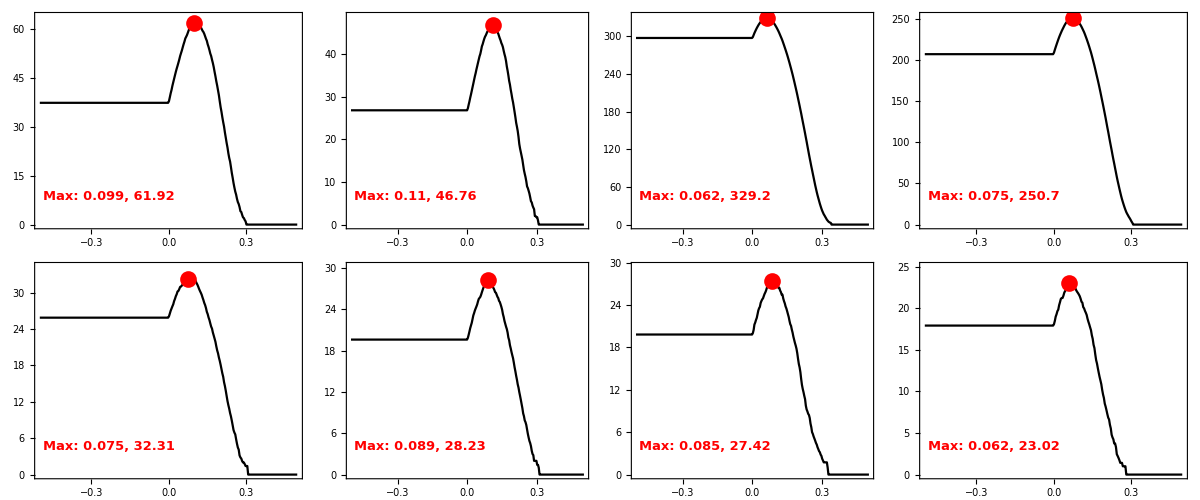
-Graphics-S/√(S + B)BDT Cut

grid2.pdf

```mathematica
data0=Import["run2/fom_0.csv","Data"];data0=Transpose[data0];
data1=Import["run2/fom_1.csv","Data"];data1=Transpose[data1];
data2=Import["run2/fom_2.csv","Data"];data2=Transpose[data2];
data3=Import["run2/fom_3.csv","Data"];data3=Transpose[data3];
data4=Import["run2/fom_4.csv","Data"];data4=Transpose[data4];
data5=Import["run2/fom_5.csv","Data"];data5=Transpose[data5];
data6=Import["run2/fom_6.csv","Data"];data6=Transpose[data6];
data7=Import["run2/fom_7.csv","Data"];data7=Transpose[data7];
alldata = {data0, data1, data2, data3, data4, data5, data6, data7};
maxima = {max[data0],max[data1],max[data2],max[data3],max[data4],max[data5],max[data6],max[data7]};

labels = {"a)", "b)","c)","d)","e)","f)","g)", "h)"};
plots = Table[ListLinePlot[alldata[[i]],PlotStyle->{Black}, PlotRange->{0,maxima[[i]][[2]] + 2}, Frame->True,FrameStyle->Directive[15, Black],Axes->False, FrameTicks->All, PlotRangePadding->{0.2,2},Epilog->{Text[Style["Max: " <>ToString@ N[maxima[[i]][[1]],2]<>", "<>ToString@N[maxima[[i]][[2]],4],13, Bold,Red],Scaled[{0.03,0.15}],{-1,0}],Red,PointSize[0.03],Point@maxima[[i]]}],{i,1,8}];
plots = Partition[plots, 4];

grid = plotGrid[plots, 1200, 500];
Labeled[grid, {"S/√(S + B)","BDT Cut"},{Left, Bottom},LabelStyle->Directive[20, Black], RotateLabel->True]
Export["grid2.pdf",%]
```

# Calculating the CP Asymmetries for Run 2

```mathematica
data20=Flatten[Import["run2/cp_0.csv","Data"]];
data21=Flatten[Import["run2/cp_1.csv","Data"]];
data22=Flatten[Import["run2/cp_2.csv","Data"]];
data23=Flatten[Import["run2/cp_3.csv","Data"]];
data24=Flatten[Import["run2/cp_4.csv","Data"]];
data25=Flatten[Import["run2/cp_5.csv","Data"]];
data26=Flatten[Import["run2/cp_6.csv","Data"]];
data27=Flatten[Import["run2/cp_7.csv","Data"]];
```

```mathematica
dpData = {data20[[1]]+data21[[1]], data20[[3]]+data21[[3]]};
dpErro = {Sqrt[data20[[2]]^2+data21[[2]]^2],Sqrt[data20[[4]]^2+data21[[4]]^2]};
𝒜DP = 𝒜[dpData[[1]],dpData[[2]]];
σ𝒜DP = σ𝒜[dpData[[1]],dpErro[[1]],dpData[[2]],dpErro[[2]]];
out[N[𝒜DP,2], N[σ𝒜DP,2] , "The D^+ asymmetry: "]
```

The D^+ asymmetry: 0.014±0.011

```mathematica
dsData = {data22[[1]]+data23[[1]], data22[[3]]+data23[[3]]};
dsErro = {Sqrt[data22[[2]]^2+data23[[2]]^2],Sqrt[data22[[4]]^2+data23[[4]]^2]};
𝒜DS = 𝒜[dsData[[1]],dsData[[2]]];
σ𝒜DS = σ𝒜[dsData[[1]],dsErro[[1]],dsData[[2]],dsErro[[2]]];
out[N[𝒜DS,2], N[σ𝒜DS,2] , "The D_s^+ asymmetry: "]
```

The D_s^+ asymmetry: -0.010±0.0023

```mathematica
dtData = {data24[[1]]+data25[[1]]+data26[[1]]+data27[[1]], data24[[3]]+data25[[3]]+data26[[3]]+data27[[3]]};
dtErro = {Sqrt[data24[[2]]^2+data25[[2]]^2+data26[[2]]^2+data27[[2]]^2],Sqrt[data24[[4]]^2+data25[[4]]^2+data26[[4]]^2+data27[[4]]^2]};
𝒜DT = 𝒜[dtData[[1]],dtData[[2]]];
σ𝒜DT = σ𝒜[dtData[[1]],dtErro[[1]],dtData[[2]],dtErro[[2]]];
out[N[𝒜DT,2], N[σ𝒜DT,2] , "The D^(*+) asymmetry: "]
```

The D^(*+) asymmetry: 0.018±0.016

# The Combined CP Asymmetry

```mathematica
data20=Flatten[Import["run2/cp_0.csv","Data"]];
data21=Flatten[Import["run2/cp_1.csv","Data"]];
data22=Flatten[Import["run2/cp_2.csv","Data"]];
data23=Flatten[Import["run2/cp_3.csv","Data"]];
data24=Flatten[Import["run2/cp_4.csv","Data"]];
data25=Flatten[Import["run2/cp_5.csv","Data"]];
data26=Flatten[Import["run2/cp_6.csv","Data"]];
data27=Flatten[Import["run2/cp_7.csv","Data"]];
data10=Flatten[Import["run1/cp_0.csv","Data"]];
data11=Flatten[Import["run1/cp_1.csv","Data"]];
data12=Flatten[Import["run1/cp_2.csv","Data"]];
data13=Flatten[Import["run1/cp_3.csv","Data"]];
data14=Flatten[Import["run1/cp_4.csv","Data"]];
data15=Flatten[Import["run1/cp_5.csv","Data"]];
data16=Flatten[Import["run1/cp_6.csv","Data"]];
data17=Flatten[Import["run1/cp_7.csv","Data"]];
```

```mathematica
dpData = {data20[[1]]+data21[[1]]+data10[[1]]+data11[[1]], data20[[3]]+data21[[3]]+data10[[3]]+data11[[3]]};
dpErro = {Sqrt[data20[[2]]^2+data21[[2]]^2+data10[[2]]^2+data11[[2]]^2],Sqrt[data20[[4]]^2+data21[[4]]^2+data10[[4]]^2+data11[[4]]^2]};
𝒜DP = 𝒜[dpData[[1]],dpData[[2]]];
σ𝒜DP = σ𝒜[dpData[[1]],dpErro[[1]],dpData[[2]],dpErro[[2]]];
out[N[𝒜DP,2], N[σ𝒜DP,2] , "The D^+ asymmetry: "]
```

The D^+ asymmetry: 0.010±0.010

```mathematica
dsData = {data22[[1]]+data23[[1]]+data12[[1]]+data13[[1]], data22[[3]]+data23[[3]]+data12[[3]]+data13[[3]]};
dsErro = {Sqrt[data22[[2]]^2+data23[[2]]^2+data12[[2]]^2+data13[[2]]^2],Sqrt[data22[[4]]^2+data23[[4]]^2+data12[[4]]^2+data13[[4]]^2]};
𝒜DS = 𝒜[dsData[[1]],dsData[[2]]];
σ𝒜DS = σ𝒜[dsData[[1]],dsErro[[1]],dsData[[2]],dsErro[[2]]];
out[N[𝒜DS,2], N[σ𝒜DS,2] , "The D_s^+ asymmetry: "]
```

The D_s^+ asymmetry: -0.012±0.0021

```mathematica
dtData = {data24[[1]]+data25[[1]]+data26[[1]]+data27[[1]]+data14[[1]]+data15[[1]]+data16[[1]]+data17[[1]], data24[[3]]+data25[[3]]+data26[[3]]+data27[[3]]+data14[[3]]+data15[[3]]+data16[[3]]+data17[[3]]};
dtErro = {Sqrt[data24[[2]]^2+data25[[2]]^2+data26[[2]]^2+data27[[2]]^2+data14[[2]]^2+data15[[2]]^2+data16[[2]]^2+data17[[2]]^2],Sqrt[data24[[4]]^2+data25[[4]]^2+data26[[4]]^2+data27[[4]]^2+data14[[4]]^2+data15[[4]]^2+data16[[4]]^2+data17[[4]]^2]};
𝒜DT = 𝒜[dtData[[1]],dtData[[2]]];
σ𝒜DT = σ𝒜[dtData[[1]],dtErro[[1]],dtData[[2]],dtErro[[2]]];
out[N[𝒜DT,2], N[σ𝒜DT,2] , "The D^(*+) asymmetry: "]
```

The D^(*+) asymmetry: 0.019±0.015